# Unit 10 - Parametric and Polar Curves

Topics covered in Unit X are listed below.

Plotting parametric curves

Neat animation examples

Plotting polar curves

Plotting polar curves with regions shaded

Combining different types of plots into one graph

## Plotting parametric curves

A plane curve can be described in parametric equations

x=x(t),y=y(t),t∈I.

where t is called the parameter and I is certain interval. Parametric equations are much more powerful in describing curves than functions y=f(x). For example, a function in Cartesian coordinate system cannot describe a circle x^2+y^2=1, but the circle can be parametrized like x=cos t, y=sin t, t∈[0,2π]; it cannot describe a parabola y^2=x,y∈(-∞,∞), either, but parametric equations can, such as, x=t^2,y=t,t∈(-∞,∞). In reality, every function, y=f(x),x∈I, can always be rewritten simply in one pair of parametric equations, i.e.,

x=t,y=f(t),t∈I.

The parametrization of a curve is not unique. In fact, there are infinitely many parametric equations for describing one curve. For example, if x=x(t) and y=y(t),t∈I, describe a curve, so do

x=x(k t),y=y(k t)

where k is any nonzero real constant with t∈I'.

Similarly, a space curve can be described in parametric equations with one parameter t

x=x(t),y=y(t),z=z(t),t∈I.

Moreover, a surface can be described in parametric equations with two parameters s and t

x=x(s,t),y=y(s,t),z=z(s,t),(s,t)∈D

where D is certain region in the s t-plane. For example, a unit sphere x^2+y^2+z^2=1 can be parametrized as

x=sin ϕ cos θ,y=sin ϕ sin θ,z=cos ϕ,θ∈[0,2π],ϕ∈[0,π].

Parametric equations play very important role in multivariable calculus.

The basic Mathematica built-in function for plotting plane curves is ParametricPlot. Typical usage includes

ParametricPlot[{x(t),y(t)},{t,t_min,t_max}], plotting one parametric curve
ParametricPlot[{{x_1(t),y_1(t)},{x_2(t),y_2(t)},…},{t,t_min,t_max}], plotting multiple parametric curves

Its version for space curves is ParametricPlot3D with same usage.

ParametricPlot3D[{x(t),y(t),z(t)},{t,t_min,t_max}]
ParametricPlot3D[{{x_1(t),y_1(t),z_1(t)},{x_2(t),y_2(t),z_2(t)},⋯},{t,t_min,t_max}]

Example 1
Use ParametricPlot to draw the circle x^2+y^2=5^2.

A parametrization of the circle is x=5 sin t, y=5 cos t,0≤t≤2π.

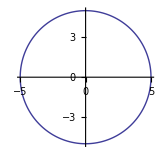

```mathematica
ParametricPlot[{5Sin[t],5Cos[t]},{t,0,2π},ImageSize->160]
```

Example 2
Use ParametricPlot to draw the circle x^2+y^2=5^2 and the ellipses x^2/3^2+y^2/4^2=1 and x^2/4^2+y^2/3^2=1.

The parametrization of the circle and the ellipses can be x=5 sin t, y=5 cos t; x=3 sin t,y=4cos t; and x=4cos t,y=3sin t, respectively, all for 0≤t≤2π.

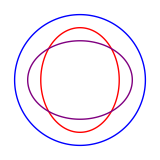

```mathematica
ParametricPlot[{{5Sin[t],5Cos[t]},{3Cos[t],4Sin[t]},{4Cos[t],3Sin[t]}},{t,0,2π},PlotStyle->{Blue,Red,Purple},Axes->None,ImageSize->160]
```

Example 3
Draw the space circle x=sin t,y= t,z=cos t,t∈[0,3π].

```mathematica
ParametricPlot3D[{Sin[t],t,Cos[t]},{t,0,3π},Ticks->None,ImageSize->160]
```

-Graphics3D-

As mentioned before, parametrization of a curve is not unique. The next two examples will exhibit this property.

Example 4
Two pairs of parametric equations, {1+2t,2+3t} and {3+2t,5+3t}, parametrize the line f(x)=3/2 x+1/2.
1. Plot the two parametric curves separately, and use GraphicsRow to display side by side.
2. Plot the two curves on one single plot.

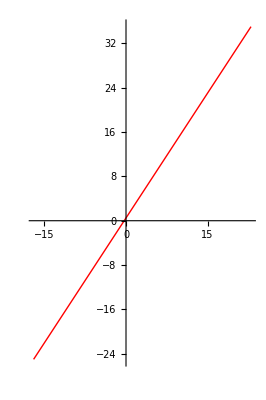

```mathematica
GraphicsRow[{
ParametricPlot[{1+2t,2+3t},{t,-10,10},ImageSize->80],
ParametricPlot[{3+2t,5+3t},{t,-10,10},PlotStyle->Red]
},Spacings->80]
```

They look as if they are exactly the same. Really? How could 1+2t=3+2t and 2+3t=5+3t hold? Theoretically, it is always better to use different symbols for the parameters used in different parametrization. Then, this question will be asking if, say, 1+2t=3+2s and 2+3t=5+3s, is a consistent system.

 Let us plot the two parametric curves on one graph to see if they coincide everywhere.

```mathematica
ParametricPlot[{{1+2t,2+3t},{3+2t,5+3t}},{t,-10,10},PlotStyle->{{Thickness[0.01],Blue},{Thickness[0.015],Dashed,Red}},ImageSize->80]
```

-Graphics-

The graph indicates that the two curves coincide everywhere except at their two ends. But as we can imagine (and experiment with expanding the plot domain), every point A(x,y) on the line can be reached (or described) by both pairs of parametric equations, but possibly at different moments, provided t denotes time.

For example, imaging a particle travels along the line. On the parametric curve of x=1+2t and y=2+3t, at the moment t=2, the particle is at (5,8); but on that of x=3+2t and y=5+3t, when the particle arrives at (5,8), it is at the moment

```mathematica
t/.NSolve[{3+2t==5,5+3t==8},t, Reals]
```

{1.}

Note: If there is no solution and our Mathematica code is correct, then the point (5,8) is not on both parametric curves and, therefore, at least one pair of parametric equations is incorrect. An easy way to tell which pair(s) is incorrect is to plot f(x)=3/2 x+1/2 together with both parametric curves. The one which seems not to coincide everywhere with f(x) is wrong.

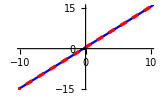

```mathematica
Show[{
Plot[3/2x+1/2,{x,-10,10},PlotStyle->Purple,ImageSize->160],
ParametricPlot[{{1+2t,2+3t},{3+2t,5+3t}},{t,-10,10},PlotStyle->{{Thickness[0.01],Blue},{Thickness[0.015],Dashed,Red}}]
}]
```

In the next animation, you can see that, at the same moment of time t, the particle arrives at different positions, following different parametric curves.

```mathematica
Manipulate[
Module[{redPoint,bluePoint},
redPoint[t_]:={1+2t,2+3t};
bluePoint[t_]:={3+2t,5+3t};
GraphicsRow[{
Show[{
ParametricPlot[redPoint[t],{t,-10,10},ImageSize->100],
Graphics[{Red, PointSize[Large],Point[redPoint[T]]}],
Graphics[{Blue, PointSize[Large],Point[bluePoint[T]]}]
}],
Module[{h=-28},
Show[{
Plot[h,{t,-15,15},PlotRange->{-30.2,30.2},Ticks->None,Axes->None,PlotStyle->White,ImageSize->160],
Graphics[{Black,Text[StringJoin["t = ", ToString[N[T,2]]],{0,h+50}]}],
Graphics[{Red,Text[StringJoin["(",ToString[redPoint[t][[1]]],", ",ToString[redPoint[t][[2]]],") = (", ToString[N[redPoint[T][[1]],2]],", ",ToString[N[redPoint[T][[2]],2]],")"],{0,h+28}]}],
Graphics[{Blue,Text[StringJoin["(",ToString[bluePoint[t][[1]]],", ",ToString[bluePoint[t][[2]]],") = (", ToString[N[bluePoint[T][[1]],2]],", ",ToString[N[bluePoint[T][[2]],2]],")"],{0,h+6}]}]
}]]
},Spacings->10]
],{{T,0,"t"},-10,10},Alignment->Center]
```

In the following animation, you can discover that, arrival at the same point on the curve, different parametric curves correspond to different moments of time t.

```mathematica
Manipulate[
Module[{redPoint,bluePoint},
redPoint[t_]:={1+2t,2+3t};
bluePoint[t_]:={3+2t,5+3t};
GraphicsRow[{
Show[{
ParametricPlot[redPoint[t],{t,-10,10},Ticks->{{-10,10},{-20,-10,10,20}},AxesLabel->{x,y},ImageSize->100],
Graphics[{Black, PointSize[Large],Point[redPoint[T]]}]
}],
Module[{h=-28},
Show[{
Plot[h,{t,-10,10},PlotRange->{-32,32},Ticks->None,Axes->None,ImageSize->120],
Graphics[{Red,PointSize[Large],Point[{T,h}]}],
Graphics[{Black,Text[StringJoin["(x, y) = (",ToString[N[redPoint[T][[1]],2]],", ",ToString[N[redPoint[T][[2]],2]],")"],{0,h+50}]}],
Graphics[{Red,Text[StringJoin["t_1 = ", ToString[N[T,2]]],{0,h+34}]}],
Module[{t},
t=t/.NSolve[bluePoint[t]==redPoint[T],t,Reals][[1]];
Show[{
Graphics[{Blue,PointSize[Large],Point[{t,h}]}],
Graphics[{Blue,Text[StringJoin["t_2 = ", ToString[N[t,2]]],{0,h+19}]}]
}]
]}]]
},Spacings->10]
],{{T,2,"x"},-10,10},Alignment->Center]
```

Example 5
Find two pairs of parametric equations which each parametrize the curve y=sin x for 0≤x≤2π.

(1) Letting x=t, we have       x=t,y=sin t,0≤t≤2π.
(2) Letting x=2t,  we obtain x=2t,y=sin 2t,0≤t≤π.

```mathematica
GraphicsRow[{
ParametricPlot[{t,Sin[t]},{t,0,2π},ImageSize->160],
ParametricPlot[{2t,Sin[2t]},{t,0,π},PlotStyle->Red]
},Spacings->40]
```

-Graphics-

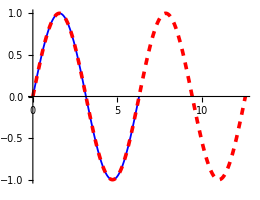

```mathematica
ParametricPlot[{{t,Sin[t]},{2t,Sin[2t]}},{t,0,2π},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.01],Dashed,Red}},ImageSize->260]
```

## Neat animation examples

To parametrize a plane (or space) curve is not very difficult. Its purpose is to describe the coordinates, x and y, of ANY point P(x,y) in terms of a chosen parameter, applying basic geometric and algebraic knowledge. A well drawn graph is usually the key to success.

In this section are four interesting examples. They exhibit the process of parametrization in detail.

Example 6 - Animating cycloid1

A cycloid is a plane curve traced out by a point P on the circumference of a circle of radius r as the circle rolls along a horizontal straight line.

Refer to the following figure. Let θ denote the angle ∠PQS. Them, |OverBar[OS]|=|PS|=r θ, and the parametric equations of point P are

x=|OverBar[OT]|=|OverBar[OS]|-|OverBar[TS]|=r θ-r sin θ=r (θ-sin θ),
 y=|OverBar[PT]|=|OverBar[RS]|=|OverBar[QS]|-|OverBar[QR]|=r-r cos θ=r (1-cos θ).

In brief,

x=r (θ-sin θ),  y=r (1-cos θ), where -∞<θ<∞.

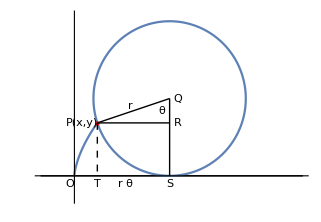

```mathematica
Manipulate[
Module[{x,y,rPoint,P}, (* xMax: length of horizontal line *)
P[r_,θ_]:={r(θ-Sin[θ]),r(1-Cos[θ])};
rPoint = 1.5(xMax/100.); (* radius of point P, relative to the scale of the horizontal line *)

Show[{
(* horizontal line and two walls at its ends *)
Plot[0,{x,-r,xMax},PlotRange->{-rPoint,2r+rPoint},Ticks->None,Axes->None,AspectRatio->Automatic,PlotStyle->{Black,Thin},ImageSize->400],
Graphics[{Black,Thin,Line[{{x,r},{x,0}}]}]/.{{x->-r},{x->xMax}},

ParametricPlot[P[r,t],{t,0,θ}],(* cycloid *)

(* rolling circle *)
{x,y}={r*θ,r};(* center of the circle *)
ParametricPlot[{x+r*Cos[t],y+ r*Sin[ t]},{t,0,2Pi},PlotStyle->Orange],
Graphics[{Orange,Line[{P[r,θ],{x,y}}]}],(* more dynamic *)
(* Table[Graphics[{LightOrange,Line[{{x+r*Cos[t],y+r*Sin[t]},{x-r*Cos[t],y-r*Sin[t]}}]}],{t,0,2π,π/12}], (* wheel *) *)

Graphics[{Red,PointSize[Large],Point[P[r,θ]]}] (* point P *)
}]
],
{{θ,0.0001},0.0001,(xMax-r)/r},
{{r,7.3*(xMax/100),"radius"},1,xMax/2},
{xMax,100,100,100,ControlType->None} 
(* This special use of xMax is a trick, somehow ugly, to get rid of using a global variable, due to the constraint of Mathematica on Animate and Manipulate *)
]
```

Example 7 - Animating hypocycloid

A hypocycloid is a plane curve traced out by a fixed point P on a circle C of radius b as C rolls without slipping on the inside of a circle with center O and radius a, where b<a.

Refer to the graph. The dashed lines are either horizontal or vertical. Let θ=∠ROS and α=∠RQP. Then, |PR|=|SR|, i.e., b α =a θ. Thus, α=a/b θ. In addition, ∠QPT= ∠CQP=∠RQP-∠RQC=α-θ=(a-b)/b θ. Therefore, using θ as the parameter, the parametric equations of P are

x=|OverBar[OB]|=|OverBar[OA]|+|OverBar[AB]|=|OverBar[OQ]|cos θ+|OverBar[TP]|=(a-b)cos θ+|OverBar[QP]| cos ∠QPT= (a-b)cos θ+b cos((a-b)/b θ),
y=|OverBar[PB]|=|OverBar[TA]|=|OverBar[QA]|-|OverBar[QT]|=|OverBar[OQ]|sin θ-|OverBar[QP]|sin ∠QPT=(a-b)sin θ-b sin((a-b)/b θ).

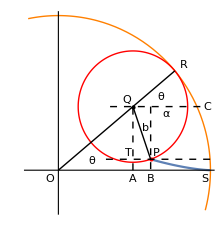

In summary,

x= (a-b)cos θ+b cos((a-b)/b θ), y=(a-b)sin θ-b sin((a-b)/b θ), where -∞<θ<∞.

```mathematica
Manipulate[
Module[{P,x,y},
P[θ_,a_,b_]:=Module[{d,q},d=a-b;q=d/b;{d*Cos[θ]+b*Cos[q*θ],d*Sin[θ]-b*Sin[q*θ]}];

Show[{
(* set up the canvas large enough to allow b > a *)
ParametricPlot[{(a+b) Cos[t],(a+b) Sin[ t]},{t,0,2Pi},Ticks->None,
AspectRatio->Automatic,PlotStyle->White,ImageSize->170],

(* the static circle *)
ParametricPlot[{a Cos[t],a Sin[ t]},{t,0,2Pi},PlotStyle->{Thick,Orange}],

ParametricPlot[P[t,a,b],{t,0,θ}],(* hypocycloid *)

(* the rolling circle *)
{x,y}={(a-b)Cos[θ],(a-b)Sin[θ]};(* center of the cicle *)
ParametricPlot[{x+b Cos[t],y+b Sin[ t]},{t,0,2Pi},PlotStyle->{Red,Thick}],
Graphics[{Red,Line[{P[θ,a,b],{x,y}}]}],(* more dynamic *)

Graphics[{Red,PointSize[Large],Point[P[ θ,a,b]]}] (* point P *)
}]
],
{{θ,π/4},0.0001,10Pi,0.1},
{{a,5},1,10}, (* a=5, b=1; a=5, b=1.1; a=2, b=3; *)
{{b,1.1},1,10}]
```

Play the animation for fun!

Example 8 - Animating epicycloid

A epicycloid is a plane curve traced out by a fixed point P on a circle C of radius b as C rolls without slipping on the outside of a circle with center O and radius a, where b<a.

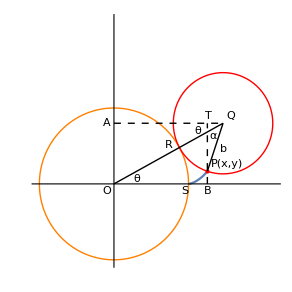

Refer to the graph. Let θ=∠QOS and α=∠OQP. Then, |PR|=|SR|, i.e., b α =a θ. Thus, α=a/b θ. Therefore, using θ as the parameter, the parametric equations of P are

x=|OverBar[AT]|=|OverBar[AQ]|-|OverBar[TQ]|=|OverBar[OQ]|cos θ-b cos(α+θ)=(a+b)cos θ-b cos((a+b)/b θ),
y=|OverBar[PB]|=|OverBar[TB]|-|OverBar[TP]|=|OverBar[AO]|-|OverBar[TP]|=|OverBar[OQ]|sin θ-b sin(α+θ)=(a+b)sin θ-b sin((a+b)/b θ).

In brief, the motion of any point P on the curve is governed by the parametric equations

x=(a+b)cos θ-b cos((a+b)/b θ), y=(a+b)sin θ-b sin((a+b)/b θ), where 0≤ θ<∞.

```mathematica
Manipulate[
Module[{P,x,y},
P[θ_,a_,b_]:=Module[{s,q},s=a+b;q=s/b;{s*Cos[θ]-b*Cos[q*θ],s*Sin[θ]-b*Sin[q*θ]}];

Show[{
(* set up the canvas large enough to allow b > a *)
ParametricPlot[{(a+2b) Cos[t],(a+2b) Sin[ t]},{t,0,2Pi},Ticks->None,
AspectRatio->Automatic,PlotStyle->White,ImageSize->170],

(* the static circle *)
ParametricPlot[{a Cos[t],a Sin[ t]},{t,0,2Pi},PlotStyle->{Thick,Orange}],

ParametricPlot[P[t,a,b],{t,0,θ}],(* epicycloid *)

(* the rolling circle *)
{x,y}={(a+b)Cos[θ],(a+b)Sin[θ]}; (* the center *)
ParametricPlot[{x+b Cos[t],y+b Sin[ t]},{t,0,2Pi},PlotStyle->{Red,Thick}],
Graphics[{Red,Line[{P[θ,a,b],{x,y}}]}],(* more dynamic *)

(* point P *)
Graphics[{Red,PointSize[Large],Point[P[θ,a,b]]}]}]
],
{{θ,π/4},0.0001,20Pi,0.1},
{{a,5},1,10}, (* a=5, b=1; a=5, b=1.1; a=2, b=3; *)
{b,1,10}]
```

Example 9
Refer to the following figure. A stick of length L can smoothly slide through a point B(b,0). Provided one end of the stick can only move along a circle with center O and radius R, find parametric equations of the path of the other end of the stick.

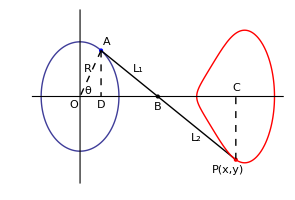

Use ∠AOB as the parameter. Draw auxiliary lines OverBar[OA], OverBar[AD], and OverBar[PC], where the latter two are each perpendicular to the x-axis. Obviously,

|OverBar[AD]|=R sin θ,
|OverBar[OD]|=R cos θ,
|OverBar[DB]|=|OverBar[OB]|-|OverBar[OD]|=b-R cos θ,
|OverBar[BC]|=|OverBar[OC]|-|OverBar[OB]|=x-b,
|OverBar[PC]|=-y.

By the Pythagorean Theorem,

L_1^2=|OverBar[AD]|^2+|OverBar[DB]|^2=(R sin θ)^2+(b-R cos θ)^2=R^2+b^2-2b R cos θ ⋯⋯⋯ (1)

Since L_1+L_2=L, we have L_2=L-L_1.

For △ABD and △PBC are similar triangles,

(|OverBar[DB]|)/L_1=(|OverBar[BC]|)/L_2, or (b-R cos θ)/L_1=(x-b)/(L-L_1)
(|OverBar[AD]|)/L_1=(|OverBar[PC]|)/L_2, or (R sin θ)/L_1=-y/(L-L_1)

Therefore,

x=b+L_2/L_1(b-R cos θ)=b+(L/L_1-1)(b-R cos θ) ⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)
y=-R(L_2/L_1)sin θ=R(1-L/L_1)sin θ ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (3)

Now, combine (1), (2), and (3), we obtain

x=b+(L/(√(R^2+b^2-2b R cos θ))-1)(b-R cos θ), y=R(1-L/(√(R^2+b^2-2b R cos θ)))sin θ, where -∞<θ<∞.

How to play with the following animation?  Click and drag the big blue point along the blue circle either clockwise or counterclockwise.

```mathematica
Manipulate[
Module[
{R=1,b=2,L=3,tmp,ymax,redPoint,f,g,theta},(* Make sure L ≥ R + b *)
If[L<R+b,Abort[]];

ymax=(L-(b-R))Sin[π/4];(* estimated value *)
theta=ArcCos[bluePoint[[1]]/Norm[bluePoint]];
If[bluePoint[[2]]<0,theta=2π-theta];(* 3rd or 4th quadrant *)
bluePoint=R{Cos[theta],Sin[theta]}; (* draw it to the circle always *)
tmp=L/Sqrt[R^2+b^2-2b *R*Cos[theta]];
redPoint={b+(tmp-1)(b-R*Cos[theta]),R(1-tmp)Sin[theta]};

Show[{
Plot[{x},{x,-R-0.1,R+L+0.1},PlotRange->{-ymax,ymax},AspectRatio->Automatic,PlotStyle->White,Ticks->None,ImageSize->350],
(* setup proper canvas so that the frame will not change during animation *)

ParametricPlot[{R Cos[θ],R Sin[θ]},{θ,0,2Pi}],
Graphics[{Blue,PointSize[Large],Point[bluePoint]}],
Graphics[{Black,PointSize[Large],Point[{b,0}]}],
Graphics[{Red,PointSize[Large],Point[redPoint]}],
Graphics[{Black,Line[{redPoint,bluePoint}]}],
Graphics[{Black,Text[O,{-0.15,-0.15}]}],
Graphics[{Black,Text[B,{b,-0.2}]}],
ParametricPlot[Module[{},
tmp=L/Sqrt[R^2+b^2-2b *R*Cos[θ]];
{b+(tmp-1)(b-R*Cos[θ]),R(1-tmp)Sin[θ]}],{θ,0,2π},PlotStyle->Red]
}]],{{bluePoint,{1,1}},Locator},Alignment->Center]
(* bluePoint doesn't have to be initialized to be on the circle since it will be drawn to it *)
```

Play with various combinations of R,b, and L. We are all good mechanical engineers today!

## Plotting polar curves

A polar curve is a special type of plane parametric curves. It is the graph of r=f(θ), where (r,θ) are standard polar coordinates defined by

x=r cos θ and y=r sin θ.

Obviously, the parameter is θ. Therefore, we can use ParametricPlot to draw the curve. For example,

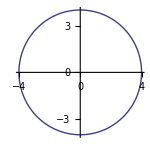

```mathematica
r[θ_]:=4;
ParametricPlot[{r[θ]Cos[θ],r[θ]Sin[θ]},{θ,0,2Pi},ImageSize->150]
```

However, since polar coordinates provide great convenience in describing some types of plane curves, and when the integrand contains patterns like x^2+y^2, they tend usually to simplify a multiple integral remarkably, polar coordinates are so important and beautiful that they deserve extra discussion and special treatment.

The basic Mathematica built-in function for plotting polar curves is PolarPlot.

Usage:
PolarPlot[r,{θ,θ_min,θ_max}] , plotting one polar curve defined by r=f(θ)
PolarPlot[{r_1,r_2,…},{θ,θ_min,θ_max}], plotting multiple polar curves defined by r_1=f_1(θ), r_2=f_2(θ),⋯

Example 10
Use PolarPlot to draw the circle x^2+y^2=4^2.

```mathematica
PolarPlot[4,{θ,0,2π},ImageSize->150]
```

-Graphics-

Example 11
Use PolarPlot to draw the circle x^2+y^2=4^2 and the polar curve r=-θ cos θ on one plot. Access Mathematica Wolfram Documentation, and play with some important options.

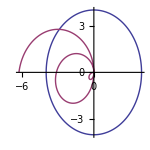

```mathematica
PolarPlot[{4,-θ Cos[θ]},{θ,0,2Pi},ImageSize->150]
```

```mathematica
PolarPlot[{4,-θ Cos[θ]},{θ,0,2Pi},Axes->None,ImageSize->150, PolarGridLines->Automatic,PlotStyle->{{Red,Thickness[0.02]},{Purple,Thickness[0.02]}}]
```

-Graphics-

```mathematica
PolarPlot[{4Cos[θ],-θ Cos[θ]},{θ,0,2Pi},ImageSize->150,PolarTicks->Automatic,GridLinesStyle->Directive[Dashed,Thin,Blue],PolarGridLines->Automatic,PlotStyle->{{Red,Thickness[0.02]},{Purple,Thickness[0.02]}}]
```

-Graphics-

Example 12. Some neat graphs.

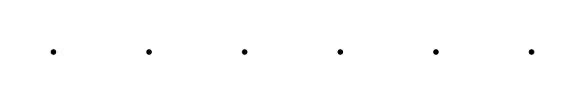

```mathematica
GraphicsRow[Table[PolarPlot[Sin[1.6θ]^2+Cos[n θ]^5, {θ,0,10π},Axes->None,ImageSize->88],{n,6}]]
```

Example 13
Rewrite the unit circle x^2+y^2=1 in polar coordinate system, and plot the polar curve.

Substituting x=r cos θ and y=r sin θ into x^2+y^2=1, we obtain r^2 cos^2 θ+r^2 sin^2 θ or r=±1. We can also let computer find the polar function r=f(θ) for us.

{-1,1}

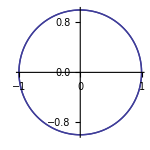

```mathematica
eqn=x^2+y^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%,{θ,0,2π},ImageSize->150]
```

Note: For the polar curve in this example, the domain [0,2π] can be [0,π]. See Question 3 for Lab 10.

Example 14
Explore the polar curve of r=sin (n θ), where n is an integer. As far as the number of “flower” petals is concerned, what conclusion can you draw about the curve when n is even and when n is odd?

```mathematica
Manipulate[
Show[{
Plot[{x},{x,-1,1},PlotRange->{-1,1},PlotStyle->White,AspectRatio->Automatic,ImageSize->160],
(* this first plot sets up the canvas so as the size of animation is still *)

PolarPlot[Sin[n θ],{θ,0,2π}]
}],{{n,4},-20,20,1,Appearance->"Open"},Alignment->Center]
```

Example 15
Animate the rotation of the curve r=1-cos θ in polar coordinate system.

The rotation is really simple to be implemented with polar coordinate system. For r=f(θ), r=f(θ+△θ) and r=f(θ-△θ) rotate clockwise and counterclockwise, respectively, provided △θ>0.

```mathematica
Manipulate[
Module[{f},
f[θ_]:=Sin[1.6θ]^2+Cos[n*θ]^5;
Show[{
Plot[{x},{x,-2.2,2.2},PlotRange->{-2.2,2.2},AspectRatio->Automatic,PlotStyle->White,Axes->None,ImageSize->300],
PolarPlot[f[θ-theta],{θ,0,10π},PlotStyle->{Blue,Thickness[0.005]}]
}]],{{theta,0,"θ"},0,20π,DefaultDuration->25},{{n,6},1,6,1},Alignment->Center]
```

## Plotting polar curves with regions shaded

Up to Mathematica version 10, the built-in function PolarPlot do not provided the convenience Plot has offered, as far as filling is concerned. In this section, we provide a function, PolarPlotPlus, which plots two polar curves with their enclosed regions over specified interval shaded. It can also plot one polar curve if one of the two polar functions is set to 0.

The region to be shaded is approximated covered by a number of “little” polygons in Cartesian coordinate system. Unless zoomed in MANY times, usually, the generated graphs seem perfect.

Usage:
r_1,r_2: Polar curves r_1=f(θ),r_2=g(θ)
θ_1,θ_2: Plot domain of polar curves
regionθ_1,regionθ_2: Shading the region bounded by the polar curves over [regionθ_1,regionθ_2].
                                    If no region to shade, use {0,0}.
rmax: PlotRange for PolarPlot, in Cartesian coordinate system, it is actually {{-rmax, rmax},{-rmax,rmax}}.
plotGridQ: True or False.
                    PolarPlotPlus can be called multiple times for shading complex region in a polar graph:
                    Show[{
                         PolarPlotPlus[⋯, True], (* this one if False if no grid is needed at all *)
                         PolarPlotPlus[⋯, False], (* all others must be False *)
                         ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯
                         PolarPlotPlus[⋯, False]}]

```mathematica
PolarPlotPlus[{r1_,r2_},{θ_,θ1_,θ2_},{regionθ1_,regionθ2_},rmax_,plotGridQ_]:=
Module[{Δθ=Pi/144},(* time-consuming if too small; but if too large, "cracks" may appear. See Exercise 10 *)
Show[{
If[plotGridQ,
PolarPlot[{r1,r2},{θ,θ1,θ2},PlotRange->rmax,ImageSize->180,
PolarTicks->Automatic,PolarGridLines->Automatic,
GridLinesStyle->Directive[Thickness[.001],Gray,Opacity[0.4]]],
PolarPlot[{r1,r2},{θ,θ1,θ2},PlotRange->rmax,ImageSize->140,PolarTicks->Automatic]],

Table[ (* shading by covering the region with many "little" polygons *)
Graphics[{Opacity[0.2],Blue,
Module[{f,g,point},
f[t_]=r1/.θ->t; g[t_]=r2/.θ->t;
point[f_,x_]:={f[x]Cos[x],f[x]Sin[x]};
Polygon[{point[f,t],point[f,t+Δθ],point[g,t+Δθ],point[g,t]}]]
}],{t,regionθ1,regionθ2-Δθ,Δθ}]
}]
]
```

Example 16
Plot the polar curve r=cos θ.

```mathematica
f[t_]:=Cos[t];
GraphicsRow[{
PolarPlotPlus[{f[θ],0},{θ,0,2π},{0,0},1.2,True],(* with grid *)
PolarPlotPlus[{f[θ],0},{θ,0,2π},{0,0},1.2,False], (* w/o grid *)
PolarPlotPlus[{f[θ],0},{θ,0,2π},{-Pi/6,Pi/6},1.2,True] (* shaded partially *)
}]
```

-Graphics-

Example 17
Plot two concentric circles with center the origin and radii 2 and 4. Shade their enclosed region in the first quadrant.

The polar curves for the circles are r=2 and r=4, respectively.

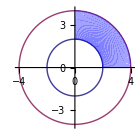

```mathematica
PolarPlotPlus[{2,4},{θ,0,2π},{0,Pi/2},4.1,False]
```

Example 18
Refer to the following graph of the polar curves r=sin θ and r=cos θ.
(1) Shade the regions B,D, and A=A'∪A'', respectively.
(2) Shade the regions C,E, and the complex region consisting of regions A,C, and E, respectively.

-Graphics-

```mathematica
(* part 1 *)
f[t_]:=Sin[t];g[t_]=Cos[t];
GraphicsRow[{
PolarPlotPlus[{f[θ],g[θ]},{θ,0,2π},{0,Pi/4},1.2,True], (* Region B *)
PolarPlotPlus[{f[θ],g[θ]},{θ,0,2π},{Pi/4,Pi/2},1.2,True], (* Region D *)
Show[{ (* Region A consists of two parts separated by a line θ=π/4 *)
PolarPlotPlus[{0,f[θ]},{θ,0,2π},{0,Pi/4},1.2,True], (* A' *)
PolarPlotPlus[{0,g[θ]},{θ,0,2π},{Pi/4,π/2},1.2,False] (* A'' *)
}]
}]
```

-Graphics-

```mathematica
(* part 2 *)
f[t_]:=Sin[t];g[t_]=Cos[t];
GraphicsRow[{
PolarPlotPlus[{0,g[θ]},{θ,0,2π},{-Pi/2,0},1.2,True], (* Region C *)
PolarPlotPlus[{f[θ],0},{θ,0,2π},{Pi/2,Pi},1.2,True], (* Region E *)
Show[{ (* Regions E, A and C *)
PolarPlotPlus[{f[θ],0},{θ,0,2π},{0,Pi/4},1.2,True],(* Region A' *)PolarPlotPlus[{0,g[θ]},{θ,0,2π},{Pi/4,π/2},1.2,False],(* Region A'' *)
PolarPlotPlus[{0,g[θ]},{θ,0,2π},{-Pi/2,0},1.2,False], (* Region C *)
PolarPlotPlus[{f[θ],0},{θ,0,2π},{Pi/2,Pi},1.2,False] (* Region E *)
}]
}]
```

-Graphics-

Example 19
Plot the polar curve r=2(1-cos 2θ) and r=4cos θ with the region outside the former and inside the latter shaded.

```mathematica
f[t_]:=2(1-Cos[2t]); g[t_]:=4Cos[t];
θ/.NSolve[f[θ]==g[θ]&&-π/2<θ<π/2,θ]
PolarPlotPlus[{f[θ],g[θ]},{θ,0,2π},%,4.5,True]
```

{-0.904557,0.904557}

-Graphics-

## Combining different types of plots into one graph

Unit 4 introduces briefly some basic skills. Indeed, it is possible to combine and merge different types of graphs into one plot. Mathematica makes the task easy through Graphics objects, including Plot, ParametricPlot, PolarPlot, ContourPlot, DiscretePlot, ListPlot, ListLinePlot, ListContourPlot, ListPolarPlot, BarChart, RectangleChart, PieChart, SectorChart, VectorPlot, and Graphics primitives (or components) such as Text, Point, Line, Disk, Circle, Rectangle, Polygon, Arrow, and so on.

Here is one more example.

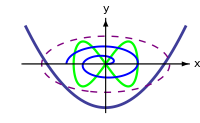

```mathematica
Show[{
Plot[1/3 x^2-7,{x,-2Pi,2Pi},PlotRange->{-7.5,7},Ticks->None,AxesLabel->{x,y},PlotStyle->Thickness[0.01],ImageSize->200],
ParametricPlot[{2.5Sin[t],3.6Sin[2t]},{t,0,2π},PlotStyle->{Green,Thickness[0.008]}],
PolarPlot[√θ,{θ,0,3π},PlotStyle->{Thickness[0.007],Blue}],
ContourPlot[x^2/5^2+(y+0.05)^2/4.5^2==1,{x,-5,5},{y,-5,5},ContourStyle->{Purple,Dashed,Thickness[0.005]}],
Graphics[{Thickness[0.001],Arrow[{{-2Pi-0.2,0},{2Pi+0.2,0}}]}],
Graphics[{Thickness[0.001],Arrow[{{0,-7.5},{0,7}}]}]
}]
```

1	Examples in the section, Neat Animation Examples, of this Unit are mainly taken from the Exercises part of Section 11.1 of Calculus, 6th edition, by James Stewart, Thomson Brooks/Cole, 2008

© 2015-2024 by David Wang, dwang@liberty.edu